## Main Function

```mathematica
BeginPackage["TwoAxisListPlot`"]
```

TwoAxisListPlot`

```mathematica
TwoAxisListPlot::usage="";
```

```mathematica
TwoAxisPlot::usage="";
```

```mathematica
ShowTwoAxisPlot::usage="";
```

```mathematica
ShowTwoAxisErrorPlot::usage="";
```

```mathematica
Begin["`Private`"]
```

TwoAxisListPlot`Private`

```mathematica
Clear[TwoAxisListPlot];
TwoAxisListPlot[f_List,g_List,{{fmx_,fMx_},{fmy_,fMy_}},{{gmx_,gMx_},{gmy_,gMy_}},opts___?OptionQ]:=Block[{old,newx,newy,scalex,scaley,newg,framecolour,framelabel,framestyle,plot1},

framestyle=Global`Colours/.{opts}/.{Global`Colours->{Table[If[d>0,{Darker[Blue,0.3],Dashing[d/100]},{Darker[Blue,0.3]}],{d,0,If[Dimensions[f]⟦1⟧==2,Dimensions[f]⟦1⟧,1]-1}],Table[If[d>0,{Darker[Red,0.3],Dashing[d/100]},{Darker[Red,0.3]}],{d,0,If[Dimensions[g]⟦1⟧==2,Dimensions[g]⟦1⟧,1]-1}]}};
framecolour=Cases[#,RGBColor[__]|GrayLevel[__],2][[1]]&/@framestyle;
scaley[var_]:=((var-gmy)*(fMy-fmy))/(gMy-gmy)+fmy;
scalex[var_]:=((var-gmx)*(fMx-fmx))/(gMx-gmx)+fmx;
newy=(ReplacePart[Prepend[Replace[Rest[#1],GrayLevel[0.]->framecolour⟦1⟧,2],scaley[First[#1]]],2->If[NumberQ[#[[2]]]&&IntegerPart[#[[2]]]==#[[2]],IntegerPart[#[[2]]],#[[2]]]]&)/@AbsoluteOptions[plot1=ListPlot[g,Frame->True,PlotRange->{{gmx,gMx},{gmy,gMy}},DisplayFunction->Identity],FrameTicks][[1,2,2]];
newx=(Prepend[Replace[Rest[#1],GrayLevel[0.]->framecolour⟦1⟧,2],scalex[First[#1]]]&)/@AbsoluteOptions[ListPlot[g,Frame->True,PlotRange->{{gmx,gMx},{gmy,gMy}},DisplayFunction->Identity],FrameTicks][[1,2,1]];
If[Dimensions[g]⟦1⟧===2,
newg=Transpose[{Map[scalex,Transpose[#][[1]],{1,2}],Map[scaley,Transpose[#][[2]],{1,2}]}]&/@g;,newg=Transpose[{Map[scalex,Transpose[g][[1]],{1,2}],Map[scaley,Transpose[g][[2]],{1,2}]}];
];
ListPlot[{If[Dimensions[f]⟦1⟧===2,Sequence@@f,f],If[Dimensions[newg]⟦1⟧===2,Sequence@@newg,newg]},
Frame->True,
FrameTicks->{Automatic,Automatic,If[{fmx,fMx}==={gmx,gMx},Automatic,newx],newy},
FrameStyle->{framecolour⟦1⟧,framecolour⟦1⟧,framecolour⟦2⟧,framecolour⟦2⟧},
FrameTicksStyle->{{framecolour⟦1⟧,framecolour⟦2⟧},{framecolour⟦1⟧,framecolour⟦2⟧}},
PlotRange->{{fmx,fMx},{fmy,fMy}}+Map[{0,0 }#&,{fMx-fmx,fMy-fmy}],
PlotStyle->Flatten[framestyle,1],
Select[{opts},#⟦1⟧=!=Global`Colours&&#⟦1⟧=!=Global`Labels&]]]
```

```mathematica
TwoAxisPlot[ffunc_Function,gfunc_Function,{{fmx_,fMx_},{fmy_,fMy_}},{{gmx_,gMx_},{gmy_,gMy_}},opts___?OptionQ]:=Block[{old,newx,newy,scalex,scaley,newg,x,f,g},
scaley[var_]:=((var-gmy)*(fMy-fmy))/(gMy-gmy)+fmy;
scalex[var_]:=((var-gmx)*(fMx-fmx))/(gMx-gmx)+fmx;
f=Cases[Plot[ffunc[x],{x,fmx,fMx}]⟦1,1,3⟧,Line[x_]->x]⟦1⟧;
g=Cases[Plot[gfunc[x],{x,gmx,gMx}]⟦1,1,3⟧,Line[x_]->x]⟦1⟧;
newy=(Prepend[Rest[#1],scaley[First[#1]]]&)/@AbsoluteOptions[ListPlot[g,Frame->True,PlotRange->grange,DisplayFunction->Identity],FrameTicks][[1,2,2]];
newx=(Prepend[Rest[#1],scalex[First[#1]]]&)/@AbsoluteOptions[ListPlot[g,Frame->True,PlotRange->grange,DisplayFunction->Identity],FrameTicks][[1,2,1]];
newg=Transpose[{Map[scalex,Transpose[g][[1]],{1,2}],Map[scaley,Transpose[g][[2]],{1,2}]}];ListPlot[{f,newg},Frame->True,FrameTicks->{Automatic,Automatic,newx,newy},FrameStyle->{Darker[Blue,0.3],Darker[Blue,0.3],Darker[Red,0.2],Darker[Red,0.2]},PlotStyle->{Blue,Darker[Red,0.2]},PlotRange->{{fmx,fMx},{fmy,fMy}}+Map[{-0.05,0.05 }#&,{fMx-fmx,fMy-fmy}],Select[{opts},#⟦1⟧=!=Colours&&#⟦1⟧=!=Labels&]]]
```

```mathematica
TwoAxisPlot[ffunc_Function,gfunc_Function,{fmx_,fMx_},{gmx_,gMx_},opts___?OptionQ]:=Block[{old,newx,newy,scalex,scaley,newg,x,f,g,fplot,gplot,fmy,fMy,gmy,gMy},
fplot=Plot[ffunc[x],{x,fmx,fMx}];
gplot=Plot[gfunc[x],{x,gmx,gMx}];
{fmy,fMy}=AbsoluteOptions[fplot,PlotRange]⟦1,2,2⟧;
{gmy,gMy}=AbsoluteOptions[gplot,PlotRange]⟦1,2,2⟧;
f=Cases[fplot⟦1,1,3⟧,Line[x_]->x]⟦1⟧;
g=Cases[gplot⟦1,1,3⟧,Line[x_]->x]⟦1⟧;
scaley[var_]:=((var-gmy)*(fMy-fmy))/(gMy-gmy)+fmy;
scalex[var_]:=((var-gmx)*(fMx-fmx))/(gMx-gmx)+fmx;
newy=(Prepend[Rest[#1],scaley[First[#1]]]&)/@AbsoluteOptions[ListPlot[g,Frame->True,PlotRange->grange,DisplayFunction->Identity],FrameTicks][[1,2,2]];
newx=(Prepend[Rest[#1],scalex[First[#1]]]&)/@AbsoluteOptions[ListPlot[g,Frame->True,PlotRange->grange,DisplayFunction->Identity],FrameTicks][[1,2,1]];
newg=Transpose[{Map[scalex,Transpose[g][[1]],{1,2}],Map[scaley,Transpose[g][[2]],{1,2}]}];ListPlot[{f,newg},Frame->True,FrameTicks->{Automatic,Automatic,newx,newy},FrameStyle->{Darker[Blue,0.3],Darker[Blue,0.3],Darker[Red,0.2],Darker[Red,0.2]},PlotStyle->{Blue,Darker[Red,0.2]},PlotRange->{{fmx,fMx},{fmy,fMy}}+Map[{-0.05,0.05 }#&,{fMx-fmx,fMy-fmy}],Select[{opts},#⟦1⟧=!=Colours&&#⟦1⟧=!=Labels&]]]
```

```mathematica
ShowTwoAxisPlot[fplot_Graphics,gplot_Graphics,opts___?OptionQ]:=Block[{old,newx,newy,scalex,scaley,newg,colour=ColorData[1,"ColorList"],x,f,g,fmx,fMx,gmx,gMx,fmy,fMy,gmy,gMy,grange,framelabel},
framelabel=Global`Labels/.{opts}/.{Global`Labels->{"","","",""}};
{{fmx,fMx},{fmy,fMy}}=AbsoluteOptions[fplot,PlotRange]⟦1,2⟧;
grange={{gmx,gMx},{gmy,gMy}}=AbsoluteOptions[gplot,PlotRange]⟦1,2⟧;
scaley[var_]:=((var-gmy)*(fMy-fmy))/(gMy-gmy)+fmy;
scalex[var_]:=((var-gmx)*(fMx-fmx))/(gMx-gmx)+fmx;
If[$VersionNumber≥9,
(*f=Flatten[Cases[fplot⟦1,2,1,3⟧,Line[x_]->x],1];
g=Flatten[Cases[gplot⟦1,2,1,3⟧,Line[x_]->x],1];*)
f=Flatten[Cases[fplot,(Line[x__]|Point[x__])->x,5],1];
g=Flatten[Cases[gplot,(Line[x__]|Point[x__])->x,5],1];,
f=Cases[fplot⟦1,1,3⟧,Line[x_]->x]⟦1⟧;
g=Cases[gplot⟦1,1,3⟧,Line[x_]->x]⟦1⟧;
];
newy=(Prepend[Rest[#1],scaley[First[#1]]]&)/@AbsoluteOptions[ListPlot[g,Frame->True,PlotRange->grange,DisplayFunction->Identity],FrameTicks][[1,2,2]];
newx=(Prepend[Rest[#1],scalex[First[#1]]]&)/@AbsoluteOptions[ListPlot[g,Frame->True,PlotRange->grange,DisplayFunction->Identity],FrameTicks][[1,2,1]];
newg=Transpose[{Map[scalex,Transpose[g][[1]],{1,2}],Map[scaley,Transpose[g][[2]],{1,2}]}];ListPlot[{f,newg},Frame->True,FrameTicks->{Automatic,Automatic,newx,newy},FrameStyle->{Darker[Blue,0.3],Darker[Blue,0.3],Darker[Red,0.2],Darker[Red,0.2]},PlotRange->{{fmx,fMx},{fmy,fMy}}+Map[{-0.05,0.05 }#&,{fMx-fmx,fMy-fmy}],FrameLabel->{framelabel⟦1⟧,framelabel⟦2⟧,framelabel⟦4⟧,framelabel⟦3⟧},PlotStyle->{Blue,Darker[Red,0.2]},Select[{opts},#⟦1⟧=!=Colours&&#⟦1⟧=!=Global`Labels&]]]
```

```mathematica
ShowTwoAxisPlot[{fplots__Graphics},{gplots__Graphics},opts___?OptionQ]:=Block[{old,newx,newy,scalex,scaley,newg,x,f,g,fmx,fMx,gmx,gMx,fmy,fMy,gmy,gMy,framelabel,plotopts,framestyles,tickstyles},
framelabel=Global`Labels/.{opts}/.{Global`Labels->{"","","",""}};
{{fmx,fMx},{fmy,fMy}}={Min[#],Max[#]}&/@Transpose[AbsoluteOptions[#,PlotRange]⟦1,2⟧&/@{fplots}];
{{gmx,gMx},{gmy,gMy}}={Min[#],Max[#]}&/@Transpose[AbsoluteOptions[#,PlotRange]⟦1,2⟧&/@{gplots}];
scaley[var_]:=((var-gmy)*(fMy-fmy))/(gMy-gmy)+fmy;
scalex[var_]:=((var-gmx)*(fMx-fmx))/(gMx-gmx)+fmx;
If[$VersionNumber≥9,
f=Cases[#⟦1,2,1,3⟧,Line[x_]->x]⟦1⟧&/@{fplots};
g=Cases[#⟦1,2,1,3⟧,Line[x_]->x]⟦1⟧&/@{gplots};,
f=Cases[#⟦1,1,3⟧,Line[x_]->x]⟦1⟧&/@{fplots};
g=Cases[#⟦1,1,3⟧,Line[x_]->x]⟦1⟧&/@{gplots};
];
newy=(Prepend[Rest[#1],scaley[First[#1]]]&)/@AbsoluteOptions[ListPlot[g,Frame->True,PlotRange->{{gmx,gMx},{gmy,gMy}},DisplayFunction->Identity],FrameTicks][[1,2,2]];
newx=(Prepend[Rest[#1],scalex[First[#1]]]&)/@AbsoluteOptions[ListPlot[g,Frame->True,PlotRange->{{gmx,gMx},{gmy,gMy}},DisplayFunction->Identity],FrameTicks][[1,2,1]];
newg=Transpose[{Map[scalex,Transpose[#][[1]],{1,2}],Map[scaley,Transpose[#][[2]],{1,2}]}]&/@g;
framestyles=If[Length[(plotopts=Select[{opts},#⟦1⟧===FrameStyle&])]>0,plotopts⟦1,2⟧,plotopts];
ListPlot[{Sequence@@f,Sequence@@newg},Frame->True,
FrameTicks->{Automatic,Automatic,NewX/.{opts}/.{NewX->newx},newy},
Select[{opts},#⟦1⟧===FrameStyle&],
FrameStyle->(Join[framestyles,{#}]&/@{Darker[Blue,0.3],Darker[Blue,0.3],Darker[Red,0.1],Darker[Red,0.1]}),
Select[{opts},#⟦1⟧===PlotRange&],
PlotRange->{{fmx,fMx},{fmy,fMy}}+Map[{-0.03,0.03 }#&,{fMx-fmx,fMy-fmy}],
FrameLabel->{framelabel⟦1⟧,framelabel⟦2⟧,framelabel⟦4⟧,framelabel⟦3⟧},

PlotStyle->Flatten[{MapIndexed[{RGBColor[0,0,0.8/#2⟦1⟧],Dashing[0.02-(#-1)/(30Length[{fplots}])],If[Length[(plotopts=Select[{opts},#⟦1⟧===PlotStyle&])]>0,plotopts⟦1,2⟧,plotopts]}&,Range[Length[{fplots}]]],Map[{Darker[Red,0.3],Dashing[0.02-(#-1)/(30Length[{gplots}])],If[Length[(plotopts=Select[{opts},#⟦1⟧===PlotStyle&])]>0,plotopts⟦1,2⟧,{}]}&,Range[Length[{gplots}]]]},1],
Select[{opts},#⟦1⟧=!=Colours&&#⟦1⟧=!=Global`Labels&&#⟦1⟧=!=NewX&]]]
```

```mathematica
ShowTwoAxisErrorPlot[fplot_Graphics,gplot_Graphics,opts___?OptionQ]:=Block[{old,newx,newy,scalex,scaley,newg,colour=ColorData[1,"ColorList"],x,f,g,fmx,fMx,gmx,gMx,fmy,fMy,gmy,gMy,grange,framelabel,fpoints,gpoints},
framelabel=Global`Labels/.{opts}/.{Global`Labels->{"","","",""}};
{{fmx,fMx},{fmy,fMy}}=AbsoluteOptions[fplot,PlotRange]⟦1,2⟧;
grange={{gmx,gMx},{gmy,gMy}}=AbsoluteOptions[gplot,PlotRange]⟦1,2⟧;
scaley[var_]:=((var-gmy)*(fMy-fmy))/(gMy-gmy)+fmy;
scalex[var_]:=((var-gmx)*(fMx-fmx))/(gMx-gmx)+fmx;
f=Cases[fplot⟦1,2,1,3⟧,Line[x_]->x]⟦1⟧;
fpoints=fplot⟦1,1,2⟧;
g=Cases[gplot⟦1,2,1,3⟧,Line[x_]->x]⟦1⟧;
gpoints=gplot⟦1,1,2⟧;
newy=(Prepend[Rest[#1],scaley[First[#1]]]&)/@AbsoluteOptions[ListPlot[g,Frame->True,PlotRange->grange,DisplayFunction->Identity],FrameTicks][[1,2,2]];
newx=(Prepend[Rest[#1],scalex[First[#1]]]&)/@AbsoluteOptions[ListPlot[g,Frame->True,PlotRange->grange,DisplayFunction->Identity],FrameTicks][[1,2,1]];
newg=Transpose[{Map[scalex,Transpose[g][[1]],{1,2}],Map[scaley,Transpose[g][[2]],{1,2}]}];ListPlot[{f,newg},Frame->True,FrameTicks->{Automatic,Automatic,newx,newy},FrameStyle->{Darker[Blue,0.3],Darker[Blue,0.3],Darker[Red,0.2],Darker[Red,0.2]},PlotRange->{{fmx,fMx},{fmy,fMy}}+Map[{-0.05,0.05 }#&,{fMx-fmx,fMy-fmy}],FrameLabel->{framelabel⟦1⟧,framelabel⟦2⟧,framelabel⟦4⟧,framelabel⟦3⟧},PlotStyle->{Blue,Darker[Red,0.2]},Select[{opts},#⟦1⟧=!=Colours&&#⟦1⟧=!=Global`Labels&],Prolog->{Blue,fpoints,Darker[Red,0.2],gpoints}]]
```

```mathematica
ShowTwoAxisErrorPlot[{fplot_Graphics,gplot_Graphics},opts___?OptionQ]:=Block[{old,newx,newy,scalex,scaley,newg,colour=ColorData[1,"ColorList"],x,f,g,fmx,fMx,gmx,gMx,fmy,fMy,gmy,gMy,grange,framelabel,fpoints,gpoints,newgpoints},
framelabel=Global`Labels/.{opts}/.{Global`Labels->{"","","",""}};
{{fmx,fMx},{fmy,fMy}}=AbsoluteOptions[fplot,PlotRange]⟦1,2⟧;
grange={{gmx,gMx},{gmy,gMy}}=AbsoluteOptions[gplot,PlotRange]⟦1,2⟧;
scaley[var_]:=((var-gmy)*(fMy-fmy))/(gMy-gmy)+fmy;
scalex[var_]:=((var-gmx)*(fMx-fmx))/(gMx-gmx)+fmx;
f=Cases[fplot⟦1,2,1,3⟧,Line[x_]->x]⟦1⟧;
fpoints=fplot⟦1,1,2⟧;
g=Cases[gplot⟦1,2,1,3⟧,Line[x_]->x]⟦1⟧;
gpoints=gplot⟦1,1,2⟧;
newgpoints={Point[Cases[gpoints⟦1⟧,{x_Real,y_Real}:>{scalex[x],scaley[y]},3]],
Chop[Map[{Cases[#,Line[{{x_,y_},{a_,b_}}]:>Line[{{scalex[x],scaley[y]},{scalex[a],scaley[b]}}],2],
Cases[#,Line[{Offset[{a_,b_},{x_,y_}],Offset[{c_,d_},{v_,w_}]}]:>Line[{Offset[{a,b},{scalex[x],scaley[y]}],Offset[{c,d},{scalex[v],scaley[w]}]}],2]}&,gpoints⟦2⟧]]
};
newy=(Prepend[Rest[#1],scaley[First[#1]]]&)/@AbsoluteOptions[gplot,FrameTicks][[1,2,2]];
newx=(Prepend[Rest[#1],scalex[First[#1]]]&)/@AbsoluteOptions[gplot,FrameTicks][[1,2,1]];
newg=Transpose[{Map[scalex,Transpose[g][[1]],{1,2}],Map[scaley,Transpose[g][[2]],{1,2}]}];ListPlot[{f,newg},Frame->True,FrameTicks->{Automatic,Automatic,newx,newy},
FrameStyle->{Darker[Blue,0.3],Darker[Blue,0.3],Darker[Red,0.2],Darker[Red,0.2]},
PlotRange->{{fmx,fMx},{fmy,fMy}}+Map[{-0.01,0.01}#&,{fMx-fmx,fMy-fmy}],FrameLabel->{framelabel⟦1⟧,framelabel⟦2⟧,framelabel⟦4⟧,framelabel⟦3⟧},PlotStyle->{Blue,Darker[Red,0.2]},Select[{opts},#⟦1⟧=!=Colours&&#⟦1⟧=!=Global`Labels&],Prolog->{Blue,fpoints,Darker[Red,0.2],newgpoints}]]
```

ListPlot[g, Frame -> True, PlotRange -> grange, DisplayFunction -> Identity]

```mathematica
End[]
```

TwoAxisListPlot`Private`

```mathematica
EndPackage[]
```

## Testing

```mathematica
Get["\\\\dlfiles03\\alice\\software\\mathematica\\TwoAxisListPlot.m"]
```

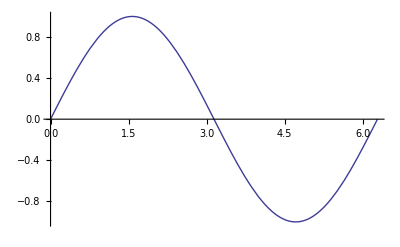

```mathematica
plot1=Plot[Sin[x],{x,0,2π}]
```

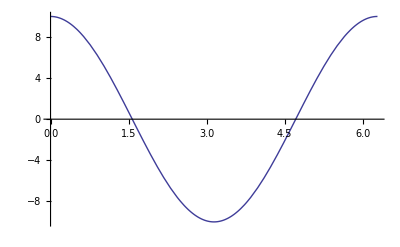

```mathematica
plot2=Plot[10Cos[x],{x,0,2π}]
```

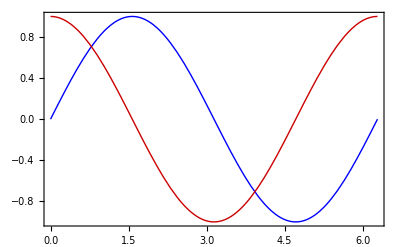

```mathematica
ShowTwoAxisPlot[plot1,plot2,Joined->True]
```